```mathematica
Clear/@{k,x,ϕ,θ,r};
Integrate[-1/(-Cosh[t]+k),{t,0,x},Assumptions->k<1&&x>0]
```

(2 ArcTan[((1+k) Tanh[x/2])/(√(1-k^2))])/(√(1-k^2))

```mathematica
ϕ[x_,k_]:=(2 ArcTan[((1+k) Tanh[x/2])/(√(1-k^2))])/(√(1-k^2));
θ[x_,k_]:=ϕ[x,k]-π/2;θ[0,0];θ[x_,-1]=Limit[θ[x,k],{k->-1}];
r[x_,k_]:=-k+Cosh[x];
```

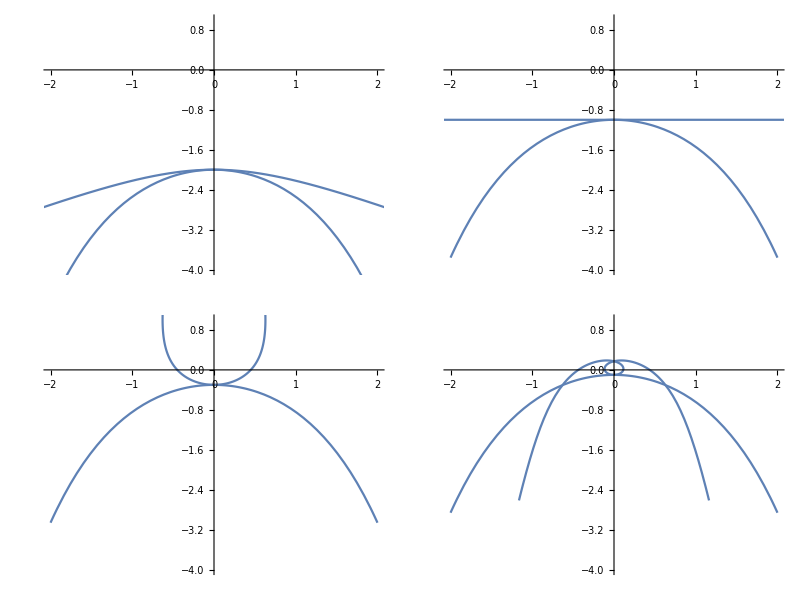

```mathematica
Grid[Partition[Table[Show[{ParametricPlot[{r[t,k]Cos[θ[t,k]],r[t,k]Sin[θ[t,k]]},{t,-2,2}],Plot[k-Cosh[x],{x,-2,2}]},PlotRange->{{-2,2},{-4,1}},AxesOrigin->{0,0}],{k,{-1,0,0.7,0.9}}],2]]
```